# Network 2 & Network 3 regenerate

## Set Environment

```mathematica
root = "~/research/posecpp/";
home = $HomeDirectory;
```

```mathematica
home = "Y:/posecpp";
```

```mathematica
home="//5.185.152.91/research/posecpp";
```

## Generate network 2

### construct network

```mathematica
rdata=ReadList[home<>"/recheck/net2_raw.txt",{Number,Number,Real,Real,Real,Real,Real,Real}];
```

```mathematica
Length[rdata]
```

487287

```mathematica
rgood1=Select[rdata,#[[2]]>100&];
```

```mathematica
Dimensions[rgood1]
```

```mathematica
rgood1[[All,5]]=Sqrt[rgood1[[All,5]]]/(Abs[rgood1[[All,8]]]);
rgood1[[All,3]]=Sqrt[rgood1[[All,3]]]/(Abs[rgood1[[All,8]]]+1);
rgood1[[All,4]]=Sqrt[rgood1[[All,4]]]/(Abs[rgood1[[All,8]]]+1);
```

```mathematica
rselected1=Select[rgood1,Total[#[[3;;5]]]<1&&Quotient[#[[1]],10000]≠Mod[#[[1]],10000]&];rgraph1=Graph[Map[Quotient[#[[1]],10000]<->Mod[#[[1]],10000]&,rselected1],VertexLabels->"Name"];
```

```mathematica
VertexCount[rgraph1]
EdgeCount[rgraph1]
```

506

2787

### plot net 2

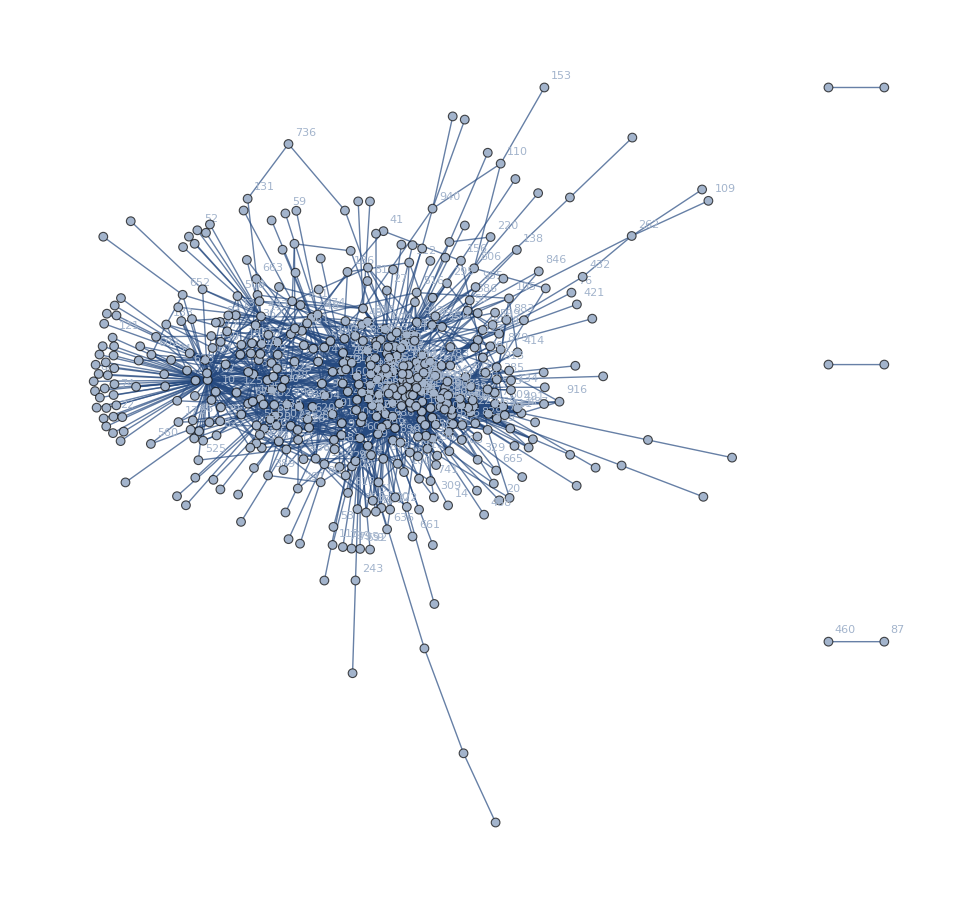

```mathematica
rgraph1
```

### test neighborhood

```mathematica
NeighborhoodGraph[rgraph1,{710},VertexLabels->"Name",ImageSize->Medium]
```

-Graphics-

```mathematica
Needs["GraphUtilities`"];
```

```mathematica
Intersection[NeighborhoodVertices[rgraph1,710,1],comm3[[3]]]
```

{496,517,693}

### Export network 2

```mathematica
Export[home<>"/recheck/net2_el.txt",EdgeList[rgraph1]]
```

//5.185.152.91/scratch/research/posecpp/recheck/net2_el.txt

## Reading Global Scale data

### read data

```mathematica
scale= ReadList[home<>"/geo/converge_s.txt",{Number,Real, Real,Real,Real, Real,Real, Real,Real,Real, Real,Real}][[;;,{1,12}]];(s[#[[1]]]=#[[2]])&/@scale;
scalemap=Select[(#->s[#])&/@Range[1006],NumberQ[#[[2]]]&];
scalemap2=Select[(#->s[#] 2)&/@Range[1006],NumberQ[#[[2]]]&];
scalemap4=Select[(#->s[#] 4)&/@Range[1006],NumberQ[#[[2]]]&];
```

```mathematica
xvr= ToExpression//@StringSplit/@ReadList[home<>"/geo/converge_x.txt",Record];
yvr= ToExpression//@StringSplit/@ReadList[home<>"/geo/converge_y.txt",Record];
svr= ToExpression//@StringSplit/@ReadList[home<>"/geo/converge_s.txt",Record];
noisyr= ToExpression//@StringSplit/@ReadList[home<>"/geo/converge_n.txt",Record]/.{false->False,true->True};
```

```mathematica
pickFinal[x_]:=x[[;;,{1,-1}]];
```

```mathematica
xvr;
```

```mathematica
xv=pickFinal[xvr];yv=pickFinal[yvr];sv=pickFinal[svr];nv=pickFinal[noisyr];summary=Join[xv,yv,sv,nv,2];
```

```mathematica
#[[1]]==#[[3]]==#[[5]]==#[[7]]&/@summary//Union
```

{True}

```mathematica
Length[summary]
```

498

```mathematica
(gx[#[[1]]]=#[[2]];gy[#[[1]]]=#[[4]];gs[#[[1]]]=#[[6]];gn[#[[1]]]=#[[8]];)&/@summary;
```

```mathematica
xmap=Select[(#->gx[#]+gs[#]/2 )&/@Range[1006],NumberQ[#[[2]]]&];
```

### data integrity verification

```mathematica
Take[summary,1]
```

{{1,0.14879,1,0.301039,1,0.732118,1,False}}

```mathematica
Table[{gs[i],s[i]},{i,1,20}]//TableForm
```

0.732118 | 0.732118
gs[2] | s[2]
0.345107 | 0.345107
gs[4] | s[4]
gs[5] | s[5]
gs[6] | s[6]
0.205269 | 0.205269
0.294197 | 0.294197
0.48478 | 0.48478
0.332886 | 0.332886
0.321082 | 0.321082
gs[12] | s[12]
0.269023 | 0.269023
gs[14] | s[14]
gs[15] | s[15]
gs[16] | s[16]
0.287021 | 0.287021
0.421231 | 0.421231
gs[19] | s[19]
gs[20] | s[20]

## Generate Network 3

### network 3 construction

```mathematica
el=Map[#[[1]]<->#[[2]]&,ReadList[home<>"/recheck/net3_el_015_02.txt",{Number,Number}]];
```

```mathematica
g3 = Graph[el,VertexLabels->"Name"];
VertexCount[g3]
EdgeCount[g3]
```

190

279

```mathematica
comm3 = FindGraphCommunities[g3]
```

{{151,861,104,208,613,746,884,118,162,785,923,637,670,751,847,314,512,523,541,744,313,354,787,947,689,771,783,798,489,538,887},{28,60,189,245,585,710,777,786,1004,422,446,914,982,997,690,688,935,702,895},{100,248,451,496,709,130,517,227,338,693,418,954,968,969,844,804,890},{223,387,605,726,261,404,735,302,946,649,919,435,701,543,839,828},{23,149,553,607,45,65,568,817,283,484,615,811},{161,294,888,938,960,291,465,764,869,583,604,886},{55,653,93,453,228,263,348,999,276,352,996},{3,889,965,225,555,518,741},{74,629,117,320,624,635,264},{91,235,316,284,488,815},{102,271,810,910,408},{556,696,872,1003},{200,580,822},{299,594,800},{439,625,680},{1,816},{39,51},{57,554},{68,961},{133,762},{147,643},{190,793},{192,673},{326,389},{362,841},{510,944},{557,559},{578,602},{601,609},{707,987},{806,922},{901,918}}

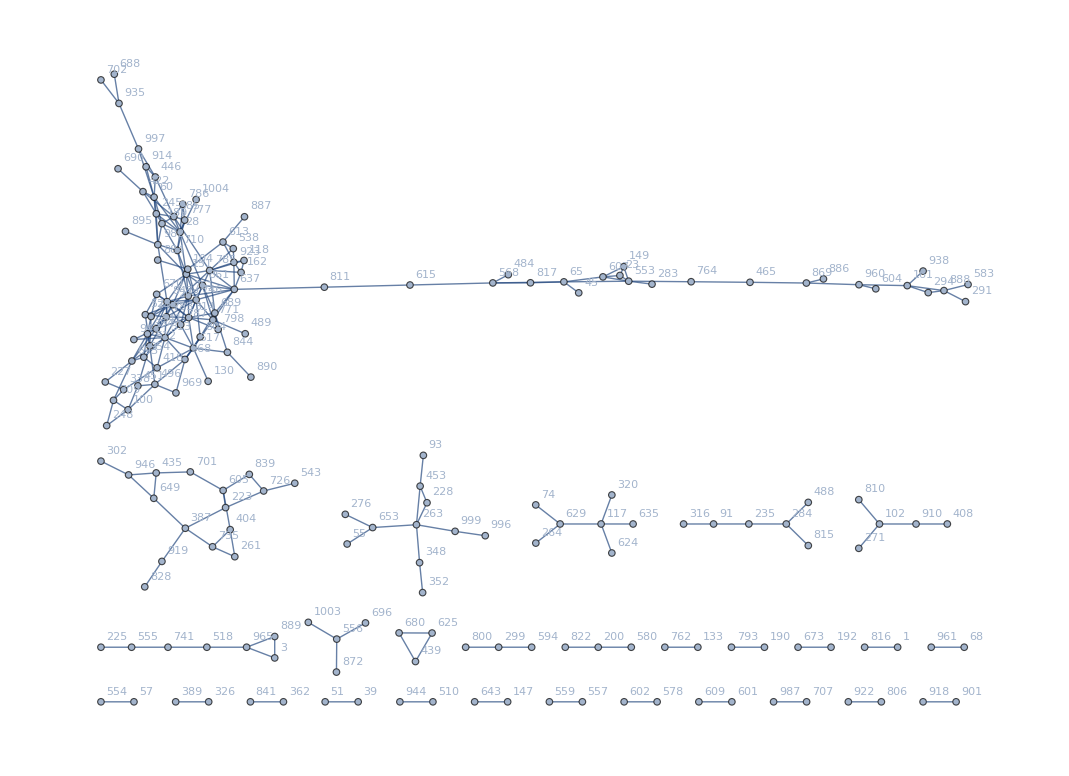

```mathematica
g3
```

```mathematica
Manipulate[TableForm[{x,Subgraph[g3,comm3[[x]]]}],{x,1,15,1}]
```

Part::partd: Part specification comm3 ⟦ 7 ⟧ is longer than depth of object.

```mathematica
HighlightGraph[g3,FindGraphCommunities[g3],VertexLabels->"",VertexSize->scalemap4]
```

-Graphics-

```mathematica
Module[{n=15},net3Comm=CommunityGraphPlot[Subgraph[g3,Union[comm3[[1;;n]]]],comm3[[1;;n]],VertexLabels->"",VertexSize->scalemap4,ImageSize->Large]]
```

-Graphics-

```mathematica
Export["D:/net3_comm.pdf",net3Comm]
```

D:/net3_comm.pdf

### relation with gdup

```mathematica
comp = ConnectedComponents[g3];
```

```mathematica
gComp1 = HighlightGraph[Subgraph[g3, comp[[1]],VertexLabels->"Name",VertexSize->scalemap2],{EdgeList[rgraph1]}~Join~ConnectedComponents[gdup],ImageSize->Large]
```

-Graphics-

### Export Plot

```mathematica
Export["D:/net3_comm.pdf",With[{comms =FindGraphCommunities[g3][[1;;8]]}, HighlightGraph[Subgraph[g3,Union[comms]],comms,VertexLabels->"",VertexSize->scalemap4,ImageSize->Large]]]
```

D:/net3_comm.pdf

```mathematica
Export["D:/net3_comm.pdf",With[{comms =FindGraphCommunities[g3][[1;;8]]}, CommunityGraphPlot[Subgraph[g3,Union[comms]],comms,VertexLabels->"",VertexSize->scalemap4,ImageSize->Large]]]
```

D:/net3_comm.pdf

## G3-G2, ideal g3

```mathematica
g32= Graph[Complement[el,Map[Quotient[#[[1]],10000]<->Mod[#[[1]],10000]&,rselected1]],VertexLabels->"Name"];
VertexCount[g32]
EdgeCount[g32]
```

175

207

```mathematica
comm32 = FindGraphCommunities[g32,Method->"CliquePercolation"];HighlightGraph[g32,comm32]
```

-Graphics-

```mathematica
HighlightGraph[Subgraph[g3, comp[[1]],VertexLabels->"Name",VertexSize->scalemap2],{EdgeList[rgraph1]}~Join~ConnectedComponents[gdup]]
```

-Graphics-

```mathematica
Subgraph[g3, comp[[1]],VertexSize->xmap]
```

-Graphics-

```mathematica
Subgraph[g3, comp[[1]],VertexLabels->xmap,ImageSize->Large]
```

-Graphics-

```mathematica
Export["D:/global_x.pdf",Subgraph[g3, comp[[1]],VertexLabels->xmap,ImageSize->Large]];
```

```mathematica
Export["D:/global_scale.pdf",HighlightGraph[Subgraph[g3, comp[[1]],VertexSize->scalemap2],{EdgeList[rgraph1]}~Join~ConnectedComponents[gdup]]];
```

```mathematica
GraphAssortativity[g3,FindGraphCommunities[g3]]//N
```

0.891432

```mathematica
Needs["GraphUtilities`"]
```

```mathematica
CommunityModularity[g3,FindGraphCommunities[g3]]
```

0.735737

## Export Core Head

```mathematica
comm[[3]]
```

{100,451,496,709}

```mathematica
Export["core_head_clusters_46.txt",{100,451,496,709}];
```

```mathematica
Export["head_clusters_46.txt",ConnectedComponents[g][[1]]]
```

head_clusters_46.txt

```mathematica
Export[ConnectedComponents[g][[1]]
```

{861,151,314,777,710,751,982,313,689,746,771,787,585,786,1004,847,895,354,517,541,693,954,844,783,785,902,208,670,744,798,890,538,923,523,512,561,162,451,724,100,496,248,709,968,338,227}

## Read Dup network

```mathematica
dupel=Map[#[[1]]<->#[[2]]&,ReadList[home<>"/recheck/dup_el_06.txt",{Number,Number}]];gdup = Graph[dupel,VertexLabels->"Name"];
```

```mathematica
HighlightGraph[Graph[dupel,VertexLabels->"Name"],{709,451,954}]
```

-Graphics-

```mathematica
HighlightGraph[gdup,Complement[VertexList[gdup],VertexList[g3]]]
```

-Graphics-

## Relations between N3 and N2

```mathematica
EdgeList[g3]//Length
EdgeList[rgraph1]//Length
```

279

3264

```mathematica
Intersection[EdgeList[g3],EdgeList[rgraph1]]//Length
```

93

```mathematica
Intersection[EdgeList[g3],EdgeList[rgraph1]]
```

{23<->553,28<->60,28<->151,28<->189,28<->245,60<->982,65<->553,65<->568,100<->248,100<->496,151<->670,151<->710,151<->751,151<->785,151<->847,161<->294,161<->888,161<->960,208<->314,208<->670,208<->744,208<->785,208<->847,227<->338,227<->693,248<->709,261<->404,294<->888,313<->314,313<->418,313<->693,313<->751,313<->847,313<->954,313<->968,314<->746,314<->751,314<->771,314<->861,338<->418,338<->709,354<->744,354<->783,354<->847,354<->954,418<->517,418<->954,435<->649,435<->701,451<->496,451<->512,465<->764,465<->869,496<->512,496<->968,496<->969,512<->744,517<->689,518<->965,523<->670,523<->744,523<->783,538<->785,538<->923,541<->693,553<->764,556<->1003,583<->888,601<->609,604<->960,605<->701,613<->923,637<->689,637<->785,649<->946,670<->744,670<->847,688<->935,689<->785,702<->935,744<->847,746<->783,746<->785,746<->847,751<->847,771<->861,787<->847,804<->968,828<->919,847<->982,869<->886,869<->960,968<->969}

```mathematica
Select[s/@VertexList[g3],NumberQ]//Mean
```

0.410806

```mathematica
Select[s/@Range[1006],NumberQ]//Mean
```

0.391131

```mathematica
Select[s/@VertexList[Graph[Intersection[EdgeList[g3],EdgeList[rgraph1]]]],NumberQ]//Mean
```

0.38864

```mathematica
Select[Range[1006],NumberQ[s[#]]&];
```

```mathematica
ginter = Graph[Intersection[EdgeList[g3],EdgeList[rgraph1]]];
```

```mathematica
HighlightGraph[Graph[Intersection[EdgeList[g3],EdgeList[rgraph1]],VertexLabels->"Name",VertexSize->(Select[(#->s[#])&/@VertexList[ginter],NumberQ[#[[2]]]&])],ConnectedComponents[gdup]]
```

-Graphics-

## Net 2 noise reduction

```mathematica
rejected=Select[rgood1,Total[#[[3;;5]]]>1.1&&Quotient[#[[1]],10000]≠Mod[#[[1]],10000]&];
```

```mathematica
Length[rejected]
```

160416

```mathematica
VertexCount[rejectedGraph]
EdgeCount[rejectedGraph]
```

VertexCount[rejectedGraph]

EdgeCount[rejectedGraph]

```mathematica
rejectedGraph=Graph[Map[Quotient[#[[1]],10000]<->Mod[#[[1]],10000]&,rejected]];
```

```mathematica
{VertexList[rejectedGraph],DegreeCentrality[rejectedGraph]}//TableForm
```

0 | 10 | 34 | 93 | 98 | 117 | 212 | 213 | 225 | 226 | 228 | 233 | 250 | 264 | 312 | 320 | 333 | 360 | 406 | 417 | 458 | 474 | 482 | 552 | 563 | 576 | 602 | 629 | 652 | 658 | 660 | 683 | 706 | 715 | 749 | 772 | 789 | 826 | 832 | 860 | 940 | 958 | 1 | 11 | 22 | 25 | 63 | 103 | 137 | 163 | 192 | 263 | 289 | 331 | 366 | 368 | 372 | 447 | 511 | 590 | 611 | 635 | 704 | 732 | 840 | 855 | 858 | 870 | 2 | 4 | 17 | 29 | 56 | 57 | 73 | 74 | 76 | 84 | 131 | 142 | 153 | 175 | 179 | 188 | 199 | 209 | 210 | 215 | 239 | 257 | 265 | 277 | 300 | 305 | 328 | 340 | 343 | 375 | 376 | 377 | 379 | 384 | 390 | 407 | 425 | 427 | 440 | 453 | 461 | 475 | 502 | 520 | 525 | 535 | 537 | 567 | 569 | 575 | 614 | 628 | 644 | 666 | 691 | 727 | 730 | 739 | 769 | 770 | 803 | 808 | 814 | 821 | 838 | 852 | 856 | 863 | 864 | 865 | 885 | 900 | 907 | 909 | 928 | 929 | 963 | 966 | 980 | 3 | 13 | 23 | 45 | 48 | 49 | 50 | 52 | 65 | 102 | 125 | 128 | 145 | 149 | 156 | 160 | 166 | 176 | 178 | 182 | 207 | 227 | 240 | 242 | 248 | 271 | 280 | 286 | 308 | 316 | 321 | 326 | 338 | 344 | 386 | 389 | 398 | 426 | 439 | 454 | 462 | 472 | 480 | 495 | 501 | 507 | 512 | 517 | 523 | 534 | 555 | 578 | 587 | 594 | 624 | 625 | 632 | 643 | 648 | 653 | 672 | 693 | 720 | 744 | 757 | 778 | 782 | 805 | 999 | 5 | 7 | 8 | 9 | 12 | 14 | 16 | 18 | 20 | 21 | 26 | 28 | 30 | 31 | 33 | 35 | 37 | 38 | 40 | 42 | 43 | 44 | 46 | 47 | 51 | 53 | 54 | 55 | 59 | 60 | 61 | 62 | 64 | 67 | 68 | 72 | 77 | 78 | 79 | 81 | 82 | 83 | 87 | 89 | 90 | 91 | 96 | 97 | 100 | 101 | 104 | 105 | 109 | 112 | 113 | 115 | 116 | 118 | 119 | 121 | 123 | 126 | 127 | 129 | 130 | 132 | 133 | 134 | 135 | 141 | 146 | 147 | 150 | 151 | 152 | 154 | 155 | 159 | 161 | 162 | 164 | 165 | 167 | 173 | 174 | 177 | 181 | 184 | 185 | 186 | 187 | 189 | 190 | 191 | 193 | 194 | 196 | 198 | 201 | 203 | 204 | 205 | 208 | 211 | 216 | 218 | 219 | 220 | 221 | 222 | 223 | 224 | 229 | 231 | 234 | 235 | 236 | 237 | 238 | 243 | 244 | 245 | 246 | 249 | 251 | 252 | 253 | 254 | 255 | 256 | 258 | 259 | 260 | 262 | 266 | 268 | 270 | 272 | 275 | 276 | 279 | 281 | 283 | 284 | 285 | 287 | 288 | 291 | 292 | 293 | 294 | 295 | 296 | 297 | 298 | 299 | 301 | 310 | 311 | 313 | 314 | 315 | 317 | 318 | 319 | 322 | 323 | 324 | 325 | 329 | 330 | 332 | 334 | 335 | 337 | 339 | 341 | 345 | 346 | 348 | 350 | 351 | 352 | 354 | 355 | 356 | 357 | 358 | 359 | 361 | 362 | 363 | 364 | 365 | 367 | 370 | 371 | 378 | 380 | 381 | 382 | 383 | 385 | 387 | 388 | 391 | 393 | 396 | 399 | 402 | 403 | 404 | 405 | 408 | 410 | 411 | 412 | 415 | 416 | 418 | 421 | 422 | 423 | 424 | 428 | 429 | 432 | 433 | 435 | 437 | 438 | 441 | 442 | 445 | 446 | 449 | 451 | 457 | 459 | 460 | 463 | 464 | 465 | 466 | 467 | 468 | 469 | 470 | 476 | 477 | 478 | 479 | 484 | 485 | 486 | 487 | 488 | 489 | 491 | 492 | 493 | 496 | 503 | 504 | 505 | 509 | 514 | 515 | 516 | 518 | 519 | 522 | 526 | 527 | 528 | 529 | 530 | 531 | 536 | 538 | 539 | 540 | 541 | 542 | 543 | 544 | 545 | 547 | 548 | 549 | 550 | 554 | 556 | 557 | 559 | 561 | 562 | 564 | 565 | 566 | 568 | 570 | 571 | 574 | 577 | 579 | 581 | 582 | 583 | 585 | 586 | 588 | 595 | 596 | 600 | 601 | 604 | 605 | 606 | 607 | 609 | 610 | 612 | 613 | 615 | 616 | 617 | 618 | 619 | 620 | 623 | 626 | 627 | 630 | 631 | 634 | 636 | 637 | 638 | 639 | 640 | 641 | 642 | 645 | 649 | 654 | 655 | 656 | 657 | 661 | 662 | 664 | 668 | 669 | 670 | 671 | 673 | 674 | 677 | 680 | 684 | 686 | 688 | 689 | 690 | 694 | 695 | 696 | 698 | 699 | 700 | 701 | 702 | 705 | 708 | 709 | 710 | 711 | 712 | 714 | 716 | 717 | 718 | 719 | 722 | 723 | 724 | 725 | 726 | 728 | 733 | 734 | 735 | 736 | 737 | 740 | 741 | 742 | 743 | 745 | 746 | 751 | 752 | 753 | 754 | 755 | 756 | 758 | 759 | 760 | 764 | 766 | 767 | 771 | 774 | 775 | 776 | 777 | 779 | 783 | 785 | 786 | 787 | 788 | 795 | 797 | 798 | 799 | 800 | 802 | 804 | 806 | 807 | 809 | 810 | 811 | 813 | 815 | 817 | 818 | 819 | 820 | 823 | 824 | 829 | 831 | 834 | 835 | 837 | 839 | 841 | 844 | 847 | 848 | 850 | 851 | 853 | 854 | 859 | 861 | 866 | 869 | 871 | 872 | 874 | 876 | 879 | 883 | 884 | 886 | 888 | 890 | 892 | 893 | 895 | 896 | 897 | 898 | 899 | 903 | 904 | 905 | 906 | 910 | 911 | 913 | 914 | 915 | 916 | 921 | 922 | 923 | 924 | 925 | 930 | 935 | 936 | 937 | 939 | 941 | 943 | 945 | 946 | 947 | 948 | 951 | 952 | 953 | 954 | 955 | 959 | 960 | 962 | 965 | 967 | 968 | 969 | 971 | 973 | 974 | 975 | 976 | 977 | 978 | 979 | 981 | 982 | 986 | 988 | 989 | 990 | 995 | 996 | 997 | 998 | 1001 | 1002 | 1004 | 15 | 19 | 32 | 39 | 41 | 66 | 69 | 71 | 86 | 94 | 95 | 106 | 107 | 110 | 114 | 120 | 122 | 124 | 136 | 138 | 140 | 143 | 144 | 148 | 168 | 169 | 171 | 183 | 195 | 200 | 202 | 217 | 230 | 241 | 247 | 261 | 267 | 278 | 290 | 302 | 303 | 306 | 309 | 327 | 336 | 374 | 392 | 395 | 397 | 401 | 409 | 414 | 420 | 431 | 434 | 448 | 455 | 471 | 481 | 483 | 490 | 500 | 506 | 508 | 513 | 532 | 551 | 553 | 560 | 572 | 573 | 580 | 584 | 589 | 591 | 592 | 597 | 598 | 599 | 608 | 621 | 622 | 647 | 650 | 659 | 665 | 667 | 685 | 692 | 707 | 713 | 729 | 748 | 762 | 768 | 773 | 784 | 791 | 793 | 794 | 796 | 801 | 816 | 827 | 828 | 830 | 833 | 842 | 843 | 845 | 846 | 857 | 862 | 877 | 878 | 882 | 887 | 889 | 894 | 901 | 902 | 912 | 917 | 918 | 919 | 920 | 931 | 934 | 938 | 942 | 949 | 956 | 961 | 964 | 970 | 972 | 987 | 994 | 1003 | 1005 | 206 | 274 | 373 | 721 | 822 | 944 | 24 | 36 | 70 | 75 | 85 | 88 | 111 | 139 | 158 | 170 | 172 | 180 | 214 | 232 | 269 | 307 | 342 | 347 | 394 | 413 | 436 | 444 | 498 | 521 | 524 | 546 | 558 | 593 | 603 | 663 | 679 | 681 | 697 | 703 | 750 | 763 | 765 | 780 | 790 | 792 | 812 | 825 | 875 | 891 | 908 | 933 | 950 | 991 | 993 | 1000 | 273 | 419 | 369 | 510 | 678 | 27 | 58 | 651 | 452 | 761 | 80 | 92 | 353 | 456 | 473 | 731 | 99 | 108 | 450 | 494 | 687 | 932 | 349 | 400 | 675 | 747 | 197 | 836 | 849 | 873 | 304 | 430 | 497 | 533 | 646 | 682 | 781 | 867 | 868 | 983 | 985 | 992 | 926 | 927 | 738 | 880
41 | 886 | 825 | 917 | 942 | 842 | 901 | 839 | 859 | 829 | 836 | 980 | 969 | 872 | 791 | 832 | 839 | 964 | 893 | 611 | 902 | 574 | 963 | 965 | 601 | 898 | 929 | 808 | 934 | 807 | 676 | 874 | 707 | 848 | 922 | 647 | 913 | 893 | 881 | 890 | 797 | 963 | 42 | 733 | 835 | 835 | 730 | 729 | 768 | 791 | 841 | 774 | 698 | 858 | 681 | 844 | 714 | 836 | 725 | 818 | 532 | 765 | 787 | 752 | 748 | 777 | 683 | 913 | 137 | 749 | 934 | 831 | 669 | 842 | 625 | 848 | 653 | 716 | 754 | 653 | 555 | 906 | 541 | 861 | 639 | 816 | 663 | 782 | 661 | 799 | 612 | 515 | 648 | 554 | 494 | 758 | 574 | 806 | 689 | 868 | 662 | 753 | 712 | 872 | 396 | 831 | 873 | 773 | 652 | 872 | 704 | 694 | 701 | 663 | 850 | 325 | 835 | 730 | 739 | 807 | 542 | 798 | 817 | 814 | 881 | 635 | 780 | 795 | 499 | 488 | 802 | 451 | 705 | 501 | 733 | 806 | 707 | 812 | 560 | 924 | 848 | 508 | 513 | 523 | 816 | 775 | 633 | 179 | 475 | 669 | 491 | 144 | 551 | 594 | 533 | 372 | 478 | 483 | 751 | 552 | 619 | 341 | 335 | 448 | 413 | 445 | 647 | 613 | 566 | 614 | 655 | 503 | 659 | 598 | 596 | 700 | 659 | 585 | 675 | 551 | 599 | 446 | 593 | 644 | 466 | 473 | 341 | 636 | 451 | 659 | 461 | 558 | 567 | 611 | 528 | 538 | 626 | 707 | 786 | 610 | 501 | 715 | 454 | 490 | 245 | 677 | 611 | 715 | 640 | 630 | 562 | 686 | 762 | 529 | 695 | 620 | 274 | 156 | 152 | 227 | 341 | 133 | 155 | 277 | 240 | 236 | 343 | 238 | 152 | 213 | 224 | 734 | 120 | 351 | 119 | 443 | 507 | 512 | 510 | 158 | 227 | 339 | 159 | 304 | 121 | 130 | 166 | 195 | 141 | 105 | 31 | 659 | 252 | 251 | 226 | 455 | 48 | 285 | 402 | 381 | 68 | 567 | 417 | 111 | 420 | 76 | 243 | 505 | 606 | 553 | 198 | 555 | 111 | 214 | 324 | 321 | 286 | 233 | 154 | 499 | 467 | 251 | 50 | 75 | 106 | 267 | 45 | 241 | 246 | 248 | 119 | 84 | 120 | 193 | 226 | 242 | 322 | 113 | 139 | 43 | 165 | 289 | 171 | 171 | 198 | 127 | 113 | 244 | 87 | 458 | 575 | 227 | 181 | 288 | 476 | 451 | 443 | 126 | 519 | 156 | 460 | 256 | 278 | 214 | 237 | 325 | 464 | 164 | 493 | 101 | 555 | 529 | 354 | 656 | 309 | 374 | 635 | 94 | 170 | 446 | 191 | 431 | 185 | 272 | 125 | 49 | 597 | 191 | 653 | 183 | 203 | 367 | 217 | 720 | 386 | 433 | 167 | 321 | 384 | 444 | 368 | 273 | 397 | 451 | 402 | 393 | 206 | 243 | 106 | 187 | 381 | 407 | 142 | 368 | 556 | 580 | 469 | 230 | 156 | 328 | 304 | 244 | 370 | 330 | 259 | 184 | 492 | 383 | 152 | 266 | 80 | 250 | 485 | 401 | 118 | 698 | 411 | 402 | 494 | 572 | 279 | 233 | 94 | 359 | 144 | 392 | 65 | 357 | 625 | 144 | 187 | 546 | 197 | 106 | 416 | 584 | 467 | 101 | 240 | 339 | 388 | 516 | 330 | 486 | 444 | 156 | 243 | 207 | 143 | 162 | 319 | 195 | 123 | 114 | 222 | 515 | 530 | 154 | 570 | 545 | 221 | 421 | 357 | 101 | 150 | 299 | 80 | 137 | 186 | 519 | 188 | 485 | 488 | 454 | 305 | 133 | 131 | 482 | 408 | 131 | 168 | 181 | 201 | 374 | 122 | 106 | 155 | 343 | 176 | 66 | 98 | 193 | 538 | 347 | 80 | 188 | 236 | 453 | 247 | 105 | 376 | 131 | 120 | 305 | 150 | 287 | 79 | 241 | 276 | 194 | 222 | 698 | 250 | 156 | 351 | 286 | 520 | 243 | 540 | 513 | 327 | 352 | 258 | 440 | 225 | 289 | 85 | 433 | 435 | 635 | 399 | 205 | 409 | 205 | 678 | 194 | 341 | 292 | 242 | 581 | 74 | 337 | 165 | 103 | 389 | 121 | 384 | 71 | 327 | 154 | 249 | 355 | 199 | 300 | 125 | 456 | 174 | 390 | 434 | 290 | 212 | 280 | 199 | 533 | 415 | 482 | 227 | 589 | 235 | 110 | 430 | 368 | 128 | 258 | 216 | 367 | 191 | 277 | 467 | 413 | 265 | 147 | 71 | 705 | 441 | 249 | 418 | 206 | 267 | 404 | 412 | 147 | 597 | 405 | 78 | 485 | 321 | 558 | 440 | 419 | 243 | 460 | 505 | 307 | 444 | 200 | 359 | 401 | 154 | 544 | 435 | 465 | 330 | 218 | 361 | 295 | 155 | 138 | 280 | 343 | 265 | 176 | 164 | 286 | 409 | 51 | 364 | 385 | 162 | 119 | 197 | 399 | 427 | 443 | 204 | 425 | 317 | 401 | 318 | 217 | 343 | 490 | 261 | 158 | 90 | 73 | 268 | 308 | 594 | 404 | 78 | 178 | 588 | 202 | 376 | 366 | 352 | 122 | 230 | 530 | 265 | 278 | 181 | 357 | 453 | 59 | 445 | 205 | 84 | 351 | 406 | 138 | 279 | 331 | 183 | 610 | 231 | 505 | 235 | 280 | 216 | 161 | 122 | 124 | 98 | 432 | 162 | 199 | 513 | 415 | 305 | 440 | 239 | 374 | 182 | 337 | 255 | 523 | 228 | 264 | 277 | 228 | 363 | 186 | 207 | 557 | 446 | 125 | 249 | 422 | 107 | 235 | 158 | 372 | 133 | 257 | 541 | 354 | 207 | 379 | 536 | 218 | 163 | 133 | 256 | 69 | 228 | 251 | 430 | 199 | 100 | 293 | 440 | 418 | 305 | 333 | 567 | 417 | 176 | 259 | 335 | 164 | 233 | 369 | 437 | 246 | 267 | 338 | 206 | 112 | 297 | 394 | 396 | 203 | 525 | 162 | 262 | 279 | 164 | 170 | 128 | 92 | 265 | 341 | 309 | 355 | 238 | 612 | 562 | 285 | 202 | 414 | 68 | 163 | 79 | 185 | 49 | 209 | 62 | 158 | 27 | 72 | 126 | 72 | 309 | 78 | 75 | 83 | 79 | 119 | 74 | 55 | 41 | 80 | 78 | 34 | 121 | 60 | 25 | 83 | 167 | 48 | 96 | 42 | 112 | 75 | 44 | 79 | 67 | 275 | 66 | 55 | 69 | 70 | 150 | 52 | 137 | 72 | 46 | 66 | 94 | 66 | 111 | 90 | 99 | 91 | 40 | 89 | 106 | 27 | 112 | 122 | 52 | 32 | 30 | 23 | 67 | 97 | 32 | 55 | 60 | 113 | 31 | 66 | 86 | 121 | 134 | 75 | 69 | 168 | 85 | 75 | 175 | 101 | 64 | 34 | 69 | 88 | 117 | 151 | 37 | 95 | 31 | 103 | 57 | 50 | 53 | 87 | 176 | 56 | 34 | 38 | 122 | 39 | 48 | 87 | 131 | 46 | 129 | 65 | 69 | 126 | 143 | 69 | 84 | 40 | 90 | 35 | 46 | 166 | 128 | 95 | 109 | 115 | 97 | 65 | 78 | 68 | 143 | 143 | 52 | 20 | 107 | 38 | 143 | 43 | 30 | 57 | 62 | 68 | 120 | 110 | 142 | 51 | 76 | 28 | 52 | 53 | 39 | 73 | 24 | 13 | 31 | 26 | 35 | 17 | 22 | 29 | 19 | 17 | 31 | 14 | 9 | 11 | 16 | 21 | 28 | 19 | 38 | 10 | 30 | 8 | 25 | 10 | 4 | 61 | 8 | 98 | 19 | 21 | 19 | 8 | 40 | 4 | 4 | 14 | 24 | 13 | 70 | 20 | 29 | 26 | 26 | 20 | 6 | 25 | 11 | 13 | 19 | 51 | 26 | 34 | 13 | 29 | 29 | 14 | 8 | 14 | 33 | 19 | 12 | 11 | 16 | 23 | 22 | 10 | 13 | 20 | 18 | 13 | 14 | 15 | 5 | 6 | 10 | 10 | 1 | 2 | 7 | 6 | 7 | 6 | 5 | 16 | 1 | 4 | 1 | 8 | 2 | 7 | 3 | 6 | 4 | 1 | 1 | 2

```mathematica
VertexDegree[rejectedGraph,225]
```

859

```mathematica
sortedBadNodes = SortBy[Transpose[{VertexList[rejectedGraph],DegreeCentrality[rejectedGraph]}],-#[[2]]&];
```

```mathematica
Length[sortedBadNodes]
```

996

```mathematica
Take[sortedBadNodes,20]
```

{{233,980},{482,969},{552,967},{958,967},{250,965},{360,962},{98,938},{652,937},{602,932},{749,932},{900,930},{789,923},{870,923},{17,918},{93,910},{458,909},{860,906},{576,903},{175,900},{826,898}}

```mathematica
nodes2 = VertexList[rgraph1];Length[nodes2]
```

506

```mathematica
Select[sortedBadNodes,MemberQ[comm2[[2]],#[[1]]]&]
```

{{312,787},{706,707},{757,691},{563,594},{693,591},{207,575},{512,564},{313,534},{886,532},{424,531},{338,515},{354,514},{695,506},{541,505},{744,504},{523,491},{869,491},{330,487},{517,483},{45,480},{847,466},{418,464},{451,460},{208,459},{472,450},{709,447},{102,441},{314,437},{804,425},{496,424},{556,418},{924,417},{954,416},{399,414},{1001,414},{888,408},{688,400},{351,399},{100,392},{559,389},{689,385},{701,381},{771,381},{283,378},{968,375},{670,374},{505,373},{465,371},{751,361},{65,358},{783,354},{583,353},{489,340},{156,330},{785,326},{960,318},{568,315},{710,307},{988,307},{861,302},{746,291},{813,278},{725,276},{254,271},{518,271},{538,269},{613,269},{605,268},{935,266},{764,261},{756,260},{261,257},{997,256},{151,255},{189,251},{866,249},{947,249},{959,249},{637,242},{20,240},{147,239},{162,233},{923,233},{990,233},{643,229},{876,227},{104,226},{528,221},{787,221},{638,215},{161,210},{982,209},{118,204},{615,200},{294,198},{922,197},{561,196},{884,196},{404,195},{371,192},{604,190},{844,190},{184,185},{446,184},{329,182},{468,181},{817,175},{798,173},{3,171},{484,169},{174,165},{467,165},{974,161},{724,160},{402,156},{478,155},{758,155},{665,149},{303,148},{1003,137},{811,135},{14,134},{1004,133},{919,121},{144,120},{842,117},{585,114},{828,112},{553,111},{965,111},{397,110},{901,108},{434,106},{890,105},{938,95},{889,87},{597,84},{134,75},{944,73},{41,62},{68,51},{794,38},{510,29},{961,17},{27,13}}

```mathematica
IncidenceList[graph22,312]
```

{312<->961}

## Net 2 Semantic Meaning

```mathematica
rselected1=Select[rgood1,Total[#[[3;;5]]]<1&&Quotient[#[[1]],10000]≠Mod[#[[1]],10000]&];rgraph1=Graph[Map[Quotient[#[[1]],10000]<->Mod[#[[1]],10000]&,rselected1],VertexLabels->"Name"];
VertexCount[rgraph1]
EdgeCount[rgraph1]
```

506

2787

```mathematica
Needs["GraphUtilities`"];
```

```mathematica
comm2 = FindGraphCommunities[rgraph1];
GraphAssortativity[rgraph1,comm2]//N
CommunityModularity[rgraph1,comm2]
```

0.558314

0.346061

```mathematica
comm2//TableForm
```

23 | 91 | 554 | 660 | 348 | 9 | 60 | 10 | 200 | 433 | 560 | 580 | 707 | 17 | 513 | 663 | 748 | 765 | 793 | 22 | 245 | 573 | 685 | 729 | 902 | 25 | 172 | 362 | 577 | 914 | 987 | 28 | 95 | 107 | 119 | 204 | 309 | 355 | 387 | 620 | 661 | 690 | 696 | 772 | 809 | 815 | 839 | 872 | 939 | 29 | 299 | 34 | 35 | 152 | 39 | 235 | 284 | 310 | 800 | 46 | 51 | 52 | 57 | 508 | 931 | 115 | 225 | 243 | 291 | 320 | 439 | 507 | 543 | 592 | 594 | 629 | 636 | 680 | 726 | 741 | 762 | 795 | 799 | 999 | 64 | 326 | 555 | 72 | 74 | 86 | 389 | 816 | 93 | 98 | 506 | 103 | 190 | 525 | 673 | 117 | 822 | 120 | 618 | 121 | 125 | 128 | 436 | 133 | 192 | 199 | 602 | 628 | 652 | 137 | 263 | 149 | 317 | 163 | 175 | 182 | 188 | 193 | 213 | 228 | 511 | 624 | 212 | 273 | 215 | 217 | 226 | 233 | 237 | 266 | 244 | 488 | 625 | 683 | 686 | 778 | 250 | 452 | 257 | 260 | 287 | 264 | 268 | 272 | 308 | 316 | 331 | 333 | 335 | 802 | 360 | 363 | 372 | 375 | 379 | 383 | 384 | 398 | 406 | 407 | 534 | 427 | 818 | 904 | 440 | 447 | 453 | 458 | 475 | 482 | 1000 | 569 | 691 | 840 | 576 | 578 | 792 | 590 | 611 | 614 | 635 | 942 | 658 | 845 | 697 | 704 | 732 | 855 | 860 | 865 | 907 | 966 | 715 | 720 | 730 | 742 | 749 | 912 | 870
688 | 886 | 924 | 3 | 156 | 161 | 399 | 424 | 465 | 518 | 568 | 583 | 643 | 888 | 922 | 960 | 100 | 207 | 338 | 451 | 496 | 709 | 14 | 523 | 935 | 20 | 102 | 151 | 294 | 585 | 637 | 710 | 889 | 890 | 938 | 965 | 1004 | 27 | 869 | 189 | 208 | 261 | 313 | 404 | 484 | 517 | 556 | 605 | 613 | 615 | 670 | 693 | 744 | 785 | 847 | 954 | 959 | 982 | 997 | 41 | 45 | 604 | 314 | 330 | 354 | 418 | 512 | 689 | 751 | 771 | 861 | 1001 | 65 | 553 | 764 | 844 | 68 | 961 | 842 | 541 | 804 | 884 | 968 | 104 | 329 | 468 | 665 | 701 | 725 | 901 | 947 | 990 | 1003 | 559 | 118 | 746 | 783 | 147 | 134 | 144 | 472 | 489 | 597 | 162 | 866 | 174 | 184 | 798 | 828 | 446 | 538 | 724 | 787 | 923 | 974 | 254 | 283 | 303 | 312 | 811 | 817 | 919 | 351 | 758 | 371 | 397 | 561 | 402 | 434 | 467 | 478 | 505 | 510 | 695 | 528 | 563 | 757 | 638 | 756 | 794 | 876 | 944 | 706 | 813 | 988 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
1 | 105 | 112 | 271 | 586 | 619 | 776 | 810 | 649 | 18 | 702 | 946 | 986 | 186 | 978 | 33 | 385 | 408 | 600 | 719 | 829 | 953 | 426 | 50 | 302 | 504 | 883 | 435 | 222 | 536 | 918 | 414 | 516 | 951 | 113 | 179 | 183 | 711 | 141 | 735 | 148 | 276 | 653 | 429 | 155 | 570 | 895 | 216 | 699 | 286 | 520 | 887 | 305 | 526 | 431 | 632 | 782 | 454 | 530 | 532 | 833 | 910 | 963 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
557 | 422 | 786 | 841 | 607 | 53 | 896 | 59 | 474 | 223 | 76 | 127 | 262 | 109 | 421 | 432 | 879 | 145 | 642 | 575 | 773 | 593 | 727 | 805 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
7 | 178 | 227 | 248 | 487 | 491 | 503 | 601 | 609 | 913 | 916 | 969 | 146 | 168 | 856 | 650 | 831 | 921 | 195 | 852 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
55 | 645 | 955 | 777 | 48 | 295 | 599 | 846 | 160 | 130 | 138 | 220 | 920 | 344 | 321 | 894 | 485 | 854 | 705 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
110 | 153 | 806 | 940 | 170 | 827 | 252 | 269 | 368 | 377 | 411 | 666 | 814 | 789 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
492 | 423 | 301 | 470 | 566 | 596 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
131 | 736 | 352 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
733 | 334 | 684 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
87 | 460 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
238 | 548 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
425 | 962 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |

```mathematica
MemberQ[#,452]&/@comm2
```

{True,False,False,False,False,False,False,False,False,False,False,False,False}

```mathematica
MemberQ[#,41]&/@comm2
```

{False,True,False,False,False,False,False,False,False,False,False,False,False}

```mathematica
Mean[Select[gs[#]&/@Range[1006],NumberQ]]
```

0.391131

```mathematica
Table[Mean[Select[gs[#]&/@comm2[[i]],NumberQ]],{i,1,8}]
```

{0.408235,0.38608,0.424435,0.470125,0.249962,0.344627,0.185,0.486575}

```mathematica
HighlightGraph[NeighborhoodGraph[rgraph1,{685},VertexLabels->"Name"],comm2[[1]]]
```

-Graphics-

```mathematica
CommunityGraphPlot[rgraph1, comm2]
```

-Graphics-

```mathematica
net2Comm=CommunityGraphPlot[rgraph1, comm2,VertexLabels->""]
```

-Graphics-

```mathematica
Export["D:/net2_comm.pdf",net2Comm]
```

D:/net2_comm.pdf

```mathematica
Length[Intersection[#,Union[comm3[[1]],comm3[[3]]]]]&/@comm2
```

{0,43,1,0,3,1,0,0,0,0,0,0,0}

```mathematica
Length/@comm2
```

{203,145,63,24,20,19,14,6,3,3,2,2,2}

```mathematica
net2Head=HighlightGraph[Subgraph[rgraph1,comm2[[2]],VertexSize->{"Nearest",2},VertexSize->EdgeForm[None],EdgeStyle->Gray],Union[comm3[[1]],comm3[[3]]], ImageSize->Large]
```

-Graphics-

```mathematica
Export["D:/net2_head.pdf",net2Head]
```

D:/net2_head.pdf

```mathematica
Length[Intersection[#,Union[comm3[[1]],comm3[[3]]]]]&/@FindGraphCommunities[Subgraph[rgraph1,comm2[[2]]]]
```

{27,3,13,0}

```mathematica
comm2[[1]]
```

{23,91,554,660,348,9,60,10,200,433,560,580,707,17,513,663,748,765,793,22,245,573,685,729,902,25,172,362,577,914,987,28,95,107,119,204,309,355,387,620,661,690,696,772,809,815,839,872,939,29,299,34,35,152,39,235,284,310,800,46,51,52,57,508,931,115,225,243,291,320,439,507,543,592,594,629,636,680,726,741,762,795,799,999,64,326,555,72,74,86,389,816,93,98,506,103,190,525,673,117,822,120,618,121,125,128,436,133,192,199,602,628,652,137,263,149,317,163,175,182,188,193,213,228,511,624,212,273,215,217,226,233,237,266,244,488,625,683,686,778,250,452,257,260,287,264,268,272,308,316,331,333,335,802,360,363,372,375,379,383,384,398,406,407,534,427,818,904,440,447,453,458,475,482,1000,569,691,840,576,578,792,590,611,614,635,942,658,845,697,704,732,855,860,865,907,966,715,720,730,742,749,912,870}

```mathematica
comm22 = FindGraphCommunities[Subgraph[rgraph1,comm2[[2]]]]
```

{{688,924,424,100,207,338,451,496,709,935,20,102,585,208,313,484,556,605,670,693,744,954,959,982,314,418,512,751,771,861,844,541,968,104,329,468,665,701,725,901,947,990,1003,746,134,489,162,446,538,923,254,817,919,467,478,505,510,757,756,794,876,944,988},{886,3,161,399,465,518,568,583,643,888,960,294,637,710,889,938,965,1004,27,869,261,404,45,604,330,689,65,553,764,68,961,842,559,147,144,174,184,798,974,283,303,312,351,371,397,434,695,638,706},{14,523,151,890,189,517,613,615,785,847,997,354,1001,804,884,118,783,866,828,724,787,811,758,561,563},{156,922,41,472,597,402,528,813}}

```mathematica
Length/@comm22
```

{63,49,25,8}

```mathematica
Intersection[#,Union[comm3[[1]],comm3[[3]]]]&/@comm22
```

{{100,104,162,208,313,314,338,418,451,489,496,512,538,541,670,693,709,744,746,751,771,844,861,923,947,954,968},{637,689,798},{118,151,354,517,523,613,783,785,787,804,847,884,890},{}}

```mathematica
HighlightGraph[Subgraph[rgraph1,comm2[[2]]],comm22,VertexLabels->"Name"]
```

-Graphics-

```mathematica
graph22=Subgraph[rgraph1,comm2[[2]],VertexLabels->"Name"];
```

```mathematica
CommunityModularity[Subgraph[rgraph1,comm2[[2]]],comm22]
```

0.238929

### k-partite

```mathematica
Length/@comm32
```

{13,9,7,5,5,4,4,3,3,3,3,3,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}

```mathematica
sub//VertexCount
```

4

```mathematica
comm32[[{3,4}]]
```

{{585,710,60,189,245,422,982},{28,585,710,777,786}}

```mathematica
pair={3,6};sub  =Subgraph[graph22,comm32[[pair]],VertexLabels->"Name"]; HighlightGraph[HighlightGraph[sub,comm32[[pair]]],dupel]
HighlightGraph[HighlightGraph[Subgraph[g3,comm32[[pair]]],comm32[[pair]]],dupel]
EdgeCount[sub]
EdgeCount[Subgraph[graph22,comm32[[#]]]]&/@pair
Length[Complement[EdgeList[Subgraph[graph22,comm32[[#]]]],dupel]]&/@pair
Intersection[VertexList[sub],#]&/@comm32[[pair]]
CommunityModularity[sub,Intersection[VertexList[sub],#]&/@comm32[[pair]]]
```

-Graphics-

-Graphics-

0

{0,0}

{0,0}

{{189,585,710,982},{553}}

SparseArray`CommunityModularity::edge weights add up to zero when EdgeWeighted->True is specified: -- Message text not found --

Part::pspec: Part specification SparseArray[Automatic, {5, 5}, 0, {1, {{0, 0, 0, 0, 0, 0}, {}}, {}}] is neither a machine-sized integer nor a list of machine-sized integers.

Part::pspec: Part specification {{3, 1, 2, 4}, {5}} is neither a machine-sized integer nor a list of machine-sized integers.

SparseArray`CommunityModularity::CommunityModularity takes a matrice: -- Message text not found --

SparseArray`CommunityModularity[{585,710,189,982,553}⟦SparseArray[<0>,{5,5}]⟧,{585,710,189,982,553}⟦{{3,1,2,4},{5}}⟧]

```mathematica
Composition
```

```mathematica
Function[x,{x,Length/@(Intersection[VertexList[Subgraph[graph22,comm32[[x]],VertexLabels->"Name"]],#]&/@comm32[[x]]),If[Length[EdgeList[Subgraph[graph22,comm32[[x]],VertexLabels->"Name"]]]==0,-10,CommunityModularity[Subgraph[graph22,comm32[[x]],VertexLabels->"Name"],Intersection[VertexList[Subgraph[graph22,comm32[[x]],VertexLabels->"Name"]],#]&/@comm32[[x]]]]}]/@Subsets[{1,2,3,4,5,7,8,10,11},{2}]
```

{{{1,2},{13,9},-0.169816},{{1,3},{13,4},-0.110162},{{1,4},{13,2},-0.0441928},{{1,5},{13,5},-0.122499},{{1,7},{13,2},-0.0498615},{{1,8},{13,3},-0.000685871},{{1,10},{13,3},-0.117066},{{1,11},{13,3},-0.106509},{{2,3},{9,4},-0.140138},{{2,4},{9,2},-0.0739645},{{2,5},{9,5},-0.1862},{{2,7},{9,2},-0.125},{{2,8},{9,3},0.},{{2,10},{9,3},-0.17301},{{2,11},{9,3},-0.2312},{{3,4},{4,2},-10},{{3,5},{4,5},-0.28125},{{3,7},{4,2},-0.5},{{3,8},{4,3},-10},{{3,10},{4,3},-0.5},{{3,11},{4,3},-0.5},{{4,5},{2,5},-0.222222},{{4,7},{2,2},-0.5},{{4,8},{2,3},-10},{{4,10},{2,3},-0.5},{{4,11},{2,3},-0.5},{{5,7},{5,2},-0.222222},{{5,8},{5,3},0.},{{5,10},{5,3},-0.382813},{{5,11},{5,3},-0.382813},{{7,8},{2,3},-10},{{7,10},{2,3},-0.5},{{7,11},{2,3},-0.5},{{8,10},{3,3},-10},{{8,11},{3,3},-10},{{10,11},{3,3},-0.5}}

```mathematica
modularities=#[[3]]&/@%
```

{-0.169816,-0.110162,-0.0441928,-0.122499,-0.0498615,-0.000685871,-0.117066,-0.106509,-0.140138,-0.0739645,-0.1862,-0.125,0.,-0.17301,-0.2312,-10,-0.28125,-0.5,-10,-0.5,-0.5,-0.222222,-0.5,-10,-0.5,-0.5,-0.222222,0.,-0.382813,-0.382813,-10,-0.5,-0.5,-10,-10,-0.5}

```mathematica
Cases[modularities,Except[-10]]
```

{-0.169816,-0.110162,-0.0441928,-0.122499,-0.0498615,-0.000685871,-0.117066,-0.106509,-0.140138,-0.0739645,-0.1862,-0.125,0.,-0.17301,-0.2312,-0.28125,-0.5,-0.5,-0.5,-0.222222,-0.5,-0.5,-0.5,-0.222222,0.,-0.382813,-0.382813,-0.5,-0.5,-0.5}

```mathematica
commtemp=Intersection[VertexList[Subgraph[graph22,comm32,VertexLabels->"Name"]],#]&/@comm32
```

{{208,313,314,354,517,541,693,746,751,783,787,847,947},{151,314,637,689,746,751,771,798,861},{189,585,710,982},{585,710},{118,162,637,785,923},{553},{446,997},{3,889,965},{},{104,208,746},{208,512,523},{},{},{},{1004},{},{},{45},{65},{},{},{},{},{817},{68},{961},{},{},{},{},{},{},{100},{},{451},{709},{102},{},{},{},{613},{884},{},{},{},{},{},{},{},{147},{643},{161},{938},{},{},{},{},{},{},{},{},{},{605},{},{},{},{},{},{261},{},{},{},{},{},{283},{},{},{},{888},{294},{},{},{},{},{},{418},{},{},{338},{},{},{},{},{919},{404},{},{},{},{484},{568},{489},{496},{},{510},{944},{844},{968},{518},{},{744},{538},{},{556},{},{},{},{559},{615},{},{},{},{},{811},{954},{},{},{804},{},{922},{890},{},{901},{},{935},{}}

```mathematica
CommunityModularity[Subgraph[graph22,Union[commtemp[[{1,2,3,4,5,7,8,10,11}]]],VertexLabels->"Name"],commtemp[[{1,2,3,4,5,7,8,10,11}]]]
```

-0.0926841

```mathematica
comm32[[2]]
```

{28,585,710,777,786,1004,60,189,245,422,446,914,997,982,690,895,935}

{{28,585,710,777,786,1004,60,189,245,422,446,914,997,982,690,895,935},{100,248,451,709,208,746,130,517,512,523,541,847,227,693,313,314,354,418,787,947,751,783,338,744,954,804},{861,118,162,785,923,151,637,689,798,489,771,844,968,890}}

```mathematica
Subsets[Range[10],{2}]
```

{{1,2},{1,3},{1,4},{1,5},{1,6},{1,7},{1,8},{1,9},{1,10},{2,3},{2,4},{2,5},{2,6},{2,7},{2,8},{2,9},{2,10},{3,4},{3,5},{3,6},{3,7},{3,8},{3,9},{3,10},{4,5},{4,6},{4,7},{4,8},{4,9},{4,10},{5,6},{5,7},{5,8},{5,9},{5,10},{6,7},{6,8},{6,9},{6,10},{7,8},{7,9},{7,10},{8,9},{8,10},{9,10}}

```mathematica
Kpartite
```

## X,y,s ploting

```mathematica
Union@@comm3[[{1,2,3}]]
```

{28,60,100,104,118,130,151,162,189,208,227,245,248,313,314,338,354,418,422,446,451,489,496,512,517,523,538,541,585,613,637,670,688,689,690,693,702,709,710,744,746,751,771,777,783,785,786,787,798,804,844,847,861,884,887,890,895,914,923,935,947,954,968,969,982,997,1004}

```mathematica
headNodeList = {#[[2]]+#[[6]]/2,-#[[4]]-#[[6]]/2}&/@Select[summary,MemberQ[Union@@comm3[[{1,2,3}]],#[[1]]]&]
```

{{0.611831,-0.23527},{0.518854,-0.291377},{0.596608,-0.083706},{0.525384,-0.17351},{0.593713,-0.232907},{0.800034,-0.151342},{0.54954,-0.160422},{0.630732,-0.228866},{0.486018,-0.230075},{0.532492,-0.134253},{0.676678,-0.033408},{0.490343,-0.248403},{0.583491,-0.0542895},{0.669813,-0.088373},{0.648539,-0.123866},{0.692763,-0.0635865},{0.585519,-0.059611},{0.727897,-0.0598525},{0.446831,-0.279854},{0.542564,-0.296248},{0.556845,-0.096139},{0.604426,-0.182399},{0.616213,-0.104647},{0.527469,-0.0814145},{0.719987,-0.111934},{0.475617,-0.080309},{0.523428,-0.233975},{0.624908,-0.090544},{0.553945,-0.24205},{0.450321,-0.205231},{0.660602,-0.194964},{0.483614,-0.12433},{0.388178,-0.302263},{0.710094,-0.156456},{0.43534,-0.255598},{0.626864,-0.036431},{0.441449,-0.358275},{0.645705,-0.0651125},{0.538356,-0.209096},{0.522304,-0.072813},{0.578304,-0.154461},{0.602851,-0.137709},{0.635458,-0.163734},{0.631552,-0.212807},{0.591654,-0.11683},{0.574528,-0.204692},{0.617165,-0.208952},{0.676203,-0.108412},{0.707962,-0.161995},{0.579894,-0.151597},{0.771662,-0.13689},{0.551753,-0.118816},{0.669272,-0.160273},{0.469118,-0.144333},{0.424175,-0.193614},{0.816526,-0.156901},{0.46646,-0.247107},{0.564305,-0.312977},{0.587323,-0.219937},{0.461674,-0.330326},{0.713201,-0.0832495},{0.661293,-0.0488175},{0.661268,-0.139992},{0.676842,-0.11955},{0.490795,-0.179642},{0.544469,-0.303925},{0.707137,-0.240235}}

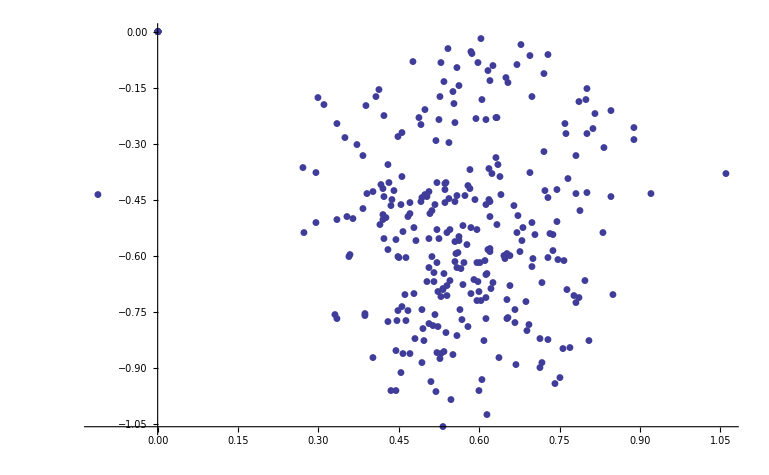

```mathematica
ListPlot[{{#[[2]]+#[[6]]/2,-#[[4]]-#[[6]]/2}&/@summary,headNodeList},PlotMarkers->Automatic]
```

```mathematica
Select[Range[15],Function[y,Length[Select[summary,MemberQ[comm3[[y]],#[[1]]]&]]>0]]
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15}

```mathematica
Table[Length[Select[summary,MemberQ[comm3[[y]],#[[1]]]&]],{y,15}]
```

{31,19,17,16,12,12,10,6,7,5,5,4,3,2,3}

```mathematica
Manipulate[ListPlot[{{#[[2]]+#[[6]]/2,-#[[4]]-#[[6]]/2}&/@summary, {#[[2]]+#[[6]]/2,-#[[4]]-#[[6]]/2}&/@Select[summary,MemberQ[comm3[[x]],#[[1]]]&]},PlotMarkers->Automatic,ImageSize->Large,PlotStyle->{Red,Blue}],{x,1,20,1}]
```

```mathematica
Manipulate[ListPlot[{{#[[2]]+#[[6]]/2,-#[[4]]-#[[6]]/2}&/@summary, {#[[2]]+#[[6]]/2,-#[[4]]-#[[6]]/2}&/@Select[summary,MemberQ[comm2[[x]],#[[1]]]&]},PlotMarkers->Automatic,ImageSize->Large,PlotStyle->{Red,Blue}],{x,1,4,1},FrameLabel->x]
```

Part::partd: Part specification comm2 ⟦ 4 ⟧ is longer than depth of object.

General::stop: Further output of Part :: partd will be suppressed during this calculation.

ListPlot::lpn: {{{0.514849, -0.667098}, {0.731928, -0.538806}, {0.652271, -0.137072}, {0.523881, -0.554454}, {0.49257, -0.443454}, {0.570035, -0.617639}, {0.588571, -0.66315}, {0.429271, -0.356315}, {0.543619, -0.664861}, {0.429076, -0.582094}, « 31 », {0.735761, -0.585324}, {0.448149, -0.744918}, {0., 0.}, {0.739775, -0.940831}, {0.595749, -0.66774}, {0.785317, -0.711982}, {0.546323, -0.985115}, {0.596608, -0.083706}, {0.522637, -0.694032}, « 448 »}, {}} is not a list of numbers or pairs of numbers.

General::stop: Further output of ListPlot :: lpn will be suppressed during this calculation.

```mathematica
For[i=1,i<5,i++,Export[("D:/net2_comm_"<>ToString[i]<>".png"),ListPlot[ {{#[[2]]+#[[6]]/2,-#[[4]]-#[[6]]/2}&/@summary, {#[[2]]+#[[6]]/2,-#[[4]]-#[[6]]/2}&/@Select[summary,MemberQ[comm2[[i]],#[[1]]]&]},PlotMarkers->{Automatic,Medium},ImageSize->Large,PlotStyle->{Gray,Red},AspectRatio->4/3]]]
```

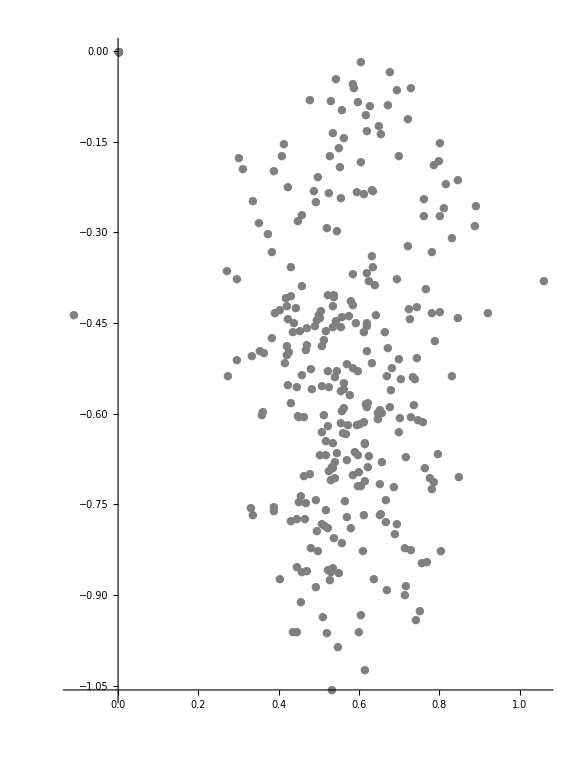

```mathematica
net2Shape=ListPlot[{{#[[2]]+#[[6]]/2,(-#[[4]]-#[[6]]/2)}&/@summary, {#[[2]]+#[[6]]/2,-#[[4]]-#[[6]]/2}&/@Select[summary,MemberQ[comm2[[2]],#[[1]]]&]},PlotMarkers->{Automatic,Medium},ImageSize->Large,PlotStyle->{Gray,Red},
AspectRatio->4/3]
```

```mathematica
Export["D:/net2_shape.tiff",net2Shape]
```

D:/net2_shape.tiff

```mathematica
Length[comm3]
```

32

```mathematica
For[i=1,i<23,i++,Export[("D:/net3_part_"<>ToString[i]<>".png"),ListPlot[ {{#[[2]]+#[[6]]/2,-#[[4]]-#[[6]]/2}&/@summary, {#[[2]]+#[[6]]/2,-#[[4]]-#[[6]]/2}&/@Select[summary,MemberQ[comm3[[i]],#[[1]]]&]},PlotMarkers->{Automatic,Medium},ImageSize->Large,PlotStyle->{Gray,Red},AspectRatio->4/3]]]
```

```mathematica
comm3[[10]]
```

{91,235,316,284,488,815}

```mathematica
comm3[[9]]
```

{74,629,117,320,624,635,264}

```mathematica
Table[Mean[Select[gs[#]&/@comm3[[i]],NumberQ]],{i,1,8}]
```

{0.384817,0.555293,0.31834,0.403415,0.35765,0.375275,0.337167,0.353342}

```mathematica
Manipulate[SortBy[Select[{#,gs[#]}&/@comm3[[i]],NumberQ[#[[2]]]&],#[[2]]&]//TableForm,{i,1,10,1}]
```

Part::partd: Part specification comm3 ⟦ 6 ⟧ is longer than depth of object.

Part::pspec: Part specification {6, gs[6]} is neither a machine-sized integer nor a list of machine-sized integers.

Part::argm: Part called with 0 arguments; 1 or more arguments are expected.

Part::partd: Part specification comm3 ⟦ 6 ⟧ is longer than depth of object.

Part::pspec: Part specification {6, gs[6]} is neither a machine-sized integer nor a list of machine-sized integers.

Part::argm: Part called with 0 arguments; 1 or more arguments are expected.

Part::partd: Part specification comm3 ⟦ 6 ⟧ is longer than depth of object.

Part::pspec: Part specification {6, gs[6]} is neither a machine-sized integer nor a list of machine-sized integers.

Part::argm: Part called with 0 arguments; 1 or more arguments are expected.

Part::partd: Part specification comm3 ⟦ 6 ⟧ is longer than depth of object.

Part::pkspec1: The expression {6, gs[6]} cannot be used as a part specification.

Part::argm: Part called with 0 arguments; 1 or more arguments are expected.

```mathematica
SortBy[Flatten[Table[Select[{#,gs[#]}&/@comm3[[i]],NumberQ[#[[2]]]&],{i,1,8}],1],#[[2]]&]//TableForm
```

227 | 0.253438
248 | 0.262521
338 | 0.265287
100 | 0.267018
496 | 0.282496
709 | 0.287393
969 | 0.290212
451 | 0.295246
55 | 0.300025
555 | 0.306397
283 | 0.308162
225 | 0.309052
653 | 0.309855
884 | 0.310068
23 | 0.310491
764 | 0.313107
149 | 0.313681
968 | 0.316378
276 | 0.316697
104 | 0.317772
489 | 0.31826
45 | 0.319253
804 | 0.322344
512 | 0.322421
130 | 0.328616
418 | 0.328743
886 | 0.329154
543 | 0.3307
869 | 0.331673
701 | 0.331724
263 | 0.332264
726 | 0.335872
607 | 0.338551
798 | 0.338859
553 | 0.339002
465 | 0.341807
348 | 0.343207
583 | 0.344617
3 | 0.345107
523 | 0.345348
228 | 0.345521
693 | 0.346334
999 | 0.347047
783 | 0.350139
960 | 0.350242
261 | 0.351137
947 | 0.354257
453 | 0.3543
605 | 0.354983
435 | 0.355053
93 | 0.356162
291 | 0.358805
518 | 0.359183
771 | 0.359297
954 | 0.359529
354 | 0.361368
223 | 0.361643
538 | 0.362732
746 | 0.363998
541 | 0.364292
517 | 0.366163
352 | 0.366591
887 | 0.367882
568 | 0.369463
923 | 0.370184
649 | 0.370194
817 | 0.37205
735 | 0.375469
888 | 0.377255
688 | 0.378689
615 | 0.379928
313 | 0.38248
208 | 0.383078
613 | 0.383389
844 | 0.383509
811 | 0.383599
118 | 0.384822
161 | 0.385071
162 | 0.38675
744 | 0.3892
935 | 0.391478
314 | 0.392688
65 | 0.392803
785 | 0.397114
965 | 0.39922
404 | 0.40045
889 | 0.401091
839 | 0.405173
787 | 0.407418
604 | 0.410339
637 | 0.410725
946 | 0.41474
689 | 0.41952
847 | 0.433425
670 | 0.433799
890 | 0.456557
484 | 0.464816
294 | 0.471691
828 | 0.475557
895 | 0.481302
938 | 0.48954
387 | 0.490362
997 | 0.491033
702 | 0.494033
751 | 0.496463
446 | 0.496942
861 | 0.500937
151 | 0.520639
690 | 0.524063
585 | 0.531961
982 | 0.545715
919 | 0.546858
302 | 0.554718
189 | 0.558487
28 | 0.569438
710 | 0.594577
422 | 0.594912
777 | 0.596821
1004 | 0.60281
786 | 0.621579
914 | 0.643847
60 | 0.705321
245 | 0.72755

## Net 2 subset for fullbody

```mathematica
fbset = Complement[Flatten[comm3[[1;;15]]],comm3[[7]]]
```

{3,23,28,45,60,65,74,91,100,102,104,117,118,130,149,151,161,162,189,200,208,223,225,227,235,245,248,261,264,271,283,284,291,294,299,302,313,314,316,320,338,354,387,404,408,418,422,435,439,446,451,465,484,488,489,496,512,517,518,523,538,541,543,553,555,556,568,580,583,585,594,604,605,607,613,615,624,625,629,635,637,649,670,680,688,689,690,693,696,701,702,709,710,726,735,741,744,746,751,764,771,777,783,785,786,787,798,800,804,810,811,815,817,822,828,839,844,847,861,869,872,884,886,887,888,889,890,895,910,914,919,923,935,938,946,947,954,960,965,968,969,982,997,1003,1004}

```mathematica
Length[fbset]
```

156

```mathematica
Export[home<>"/fullbody/nodes.txt",fbset]
```

Y:/posecpp/fullbody/nodes.txt

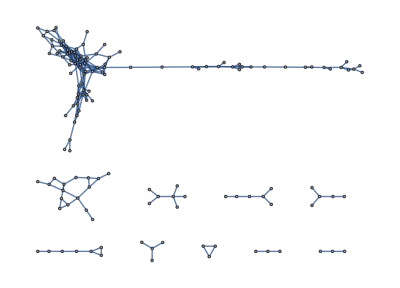

```mathematica
Subgraph[g3,fbset]
```

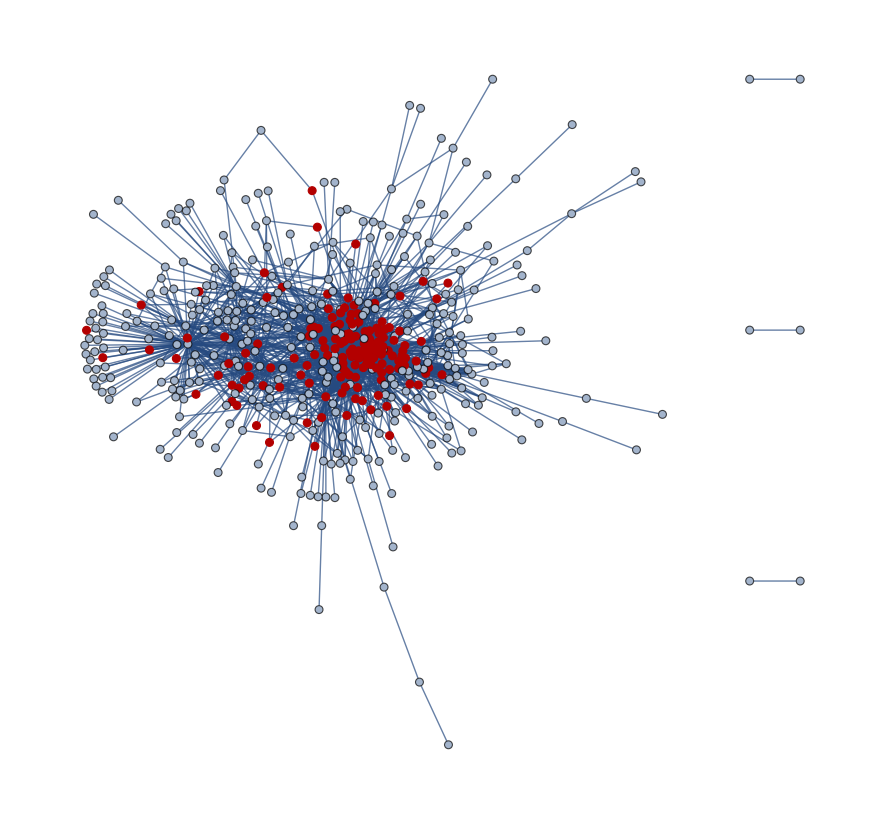

```mathematica
HighlightGraph[Graph[rgraph1,VertexLabels->""],fbset]
```

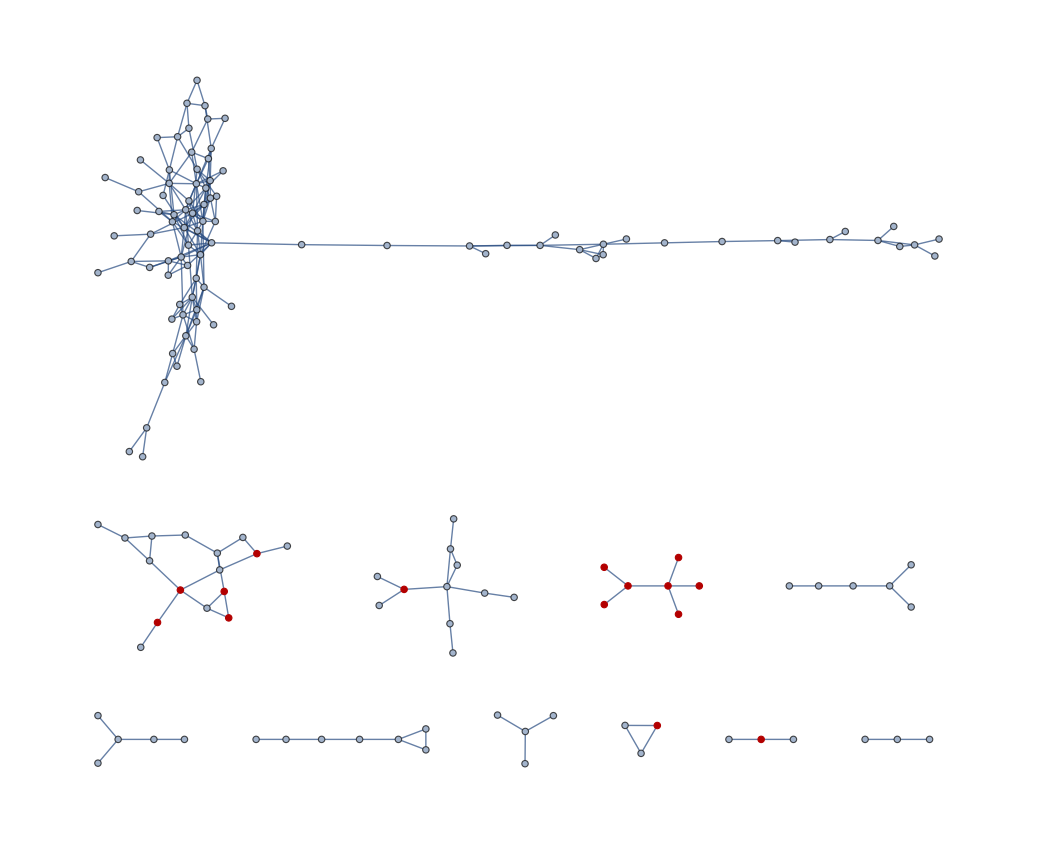

```mathematica
HighlightGraph[Subgraph[g3,Flatten[comm3[[1;;15]]]],{261,117,220,629,299,320,74,264,624,387,919,625,726,635,404,653}]
```

## Head Node Discovery

```mathematica
partSelect[x1_,x2_,y1_,y2_]:=Select[{#[[2]]+#[[6]]/2,-#[[4]]-#[[6]]/2,#[[1]]}&/@summary,x1<#[[1]]<x2&& y1<#[[2]]<y2 &]
```

```mathematica
partSelectDenoised[x1_,x2_,y1_,y2_]:=Select[{#[[2]]+#[[6]]/2,-#[[4]]-#[[6]]/2,#[[1]]}&/@Select[summary,!#[[-1]]&],x1<#[[1]]<x2&& y1<#[[2]]<y2 &]
```

```mathematica
legs = partSelect[0.5,0.7,-1,-0.6][[;;,3]]
```

{1,10,11,17,29,34,35,64,73,74,93,98,102,103,105,112,117,128,138,156,183,186,188,190,191,199,200,212,213,228,233,244,250,262,264,265,271,286,301,310,311,320,329,331,333,344,368,372,385,407,424,427,447,453,458,468,470,513,520,525,556,563,569,580,586,590,597,614,620,624,628,629,635,658,663,665,666,691,696,704,719,725,743,749,757,782,789,810,813,814,816,822,865,891,894,901,907,910,918,951,962,990,1003}

```mathematica
legsDenoised = partSelectDenoised[0.5,0.7,-1,-0.6][[;;,3]]
```

{1,10,29,34,35,64,73,74,93,98,102,103,105,112,117,128,138,156,183,186,188,190,191,199,200,212,213,228,233,244,250,262,264,265,271,286,301,310,311,320,329,331,333,368,372,385,407,424,427,447,453,458,468,470,513,520,525,556,563,569,580,586,590,597,614,620,624,628,629,635,658,663,665,666,691,696,704,719,725,743,757,782,789,810,813,814,816,822,865,891,894,901,907,910,951,962,990,1003}

```mathematica
Length/@{legs,legsDenoised}
```

{103,98}

```mathematica
Complement[legs,legsDenoised]
```

{11,17,344,749,918}

```mathematica
Export[home<>"/fullbody/legs_raw.txt",partSelect[0.5,0.7,-1,-0.6][[;;,3]]];
```

```mathematica
summary[[1]]
```

{1,0.14879,1,0.301039,1,0.732118,1,False}

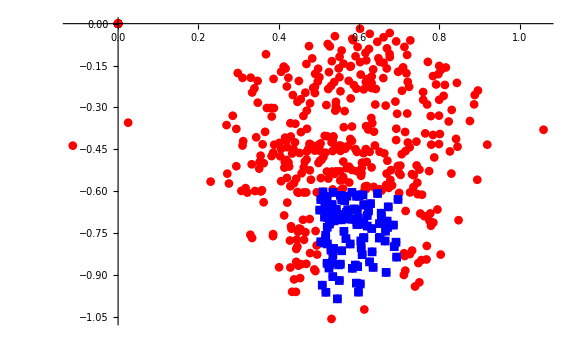

```mathematica
ListPlot[{{#[[2]]+#[[6]]/2,-#[[4]]-#[[6]]/2}&/@summary, {#[[2]]+#[[6]]/2,-#[[4]]-#[[6]]/2}&/@Select[summary,MemberQ[legs,#[[1]]]&]},PlotMarkers->Automatic,ImageSize->Large,PlotStyle->{Red,Blue}]
```

```mathematica
!summary[[-1,-1]]
```

True

```mathematica
Complement[legs, fbset]
```

{1,10,11,17,29,34,35,64,73,93,98,103,105,112,128,138,156,183,186,188,190,191,199,212,213,228,233,244,250,262,265,286,301,310,311,329,331,333,344,368,372,385,407,424,427,447,453,458,468,470,513,520,525,563,569,586,590,597,614,620,628,658,663,665,666,691,704,719,725,743,749,757,782,789,813,814,816,865,891,894,901,907,918,951,962,990}

```mathematica
Export[home<>"/fullbody/legs_raw.txt",Complement[legsDenoised, fbset]];
```